```mathematica
width = 41;
height =41;
dx = 0.01;
dy = 0.01;
grid=Table[{i*dx,j*dy},{i,1,width},{j,1,height}];
ghostarray=Table[0.0,width+2,height+2];
laplacian[array_]:={
lparray=array;
ghostarray⟦2;;-2,2;;-2⟧=array⟦;;,;;⟧;
ghostarray⟦2;;-2,1⟧ = array⟦;;,1⟧;
ghostarray⟦2;;-2,-1⟧ = array⟦;;,-1⟧;
ghostarray⟦1,2;;-2⟧ = array⟦1,;;⟧;
ghostarray⟦-1,2;;-2⟧ = array⟦-1,;;⟧;
lparray⟦;;,;;⟧=(ghostarray⟦3;;-1,2;;-2⟧+ghostarray⟦1;;-3,2;;-2⟧-2ghostarray⟦2;;-2,2;;-2⟧)/dx^2+(ghostarray⟦2;;-2,3;;-1⟧+ghostarray⟦2;;-2,1;;-3⟧-2ghostarray⟦2;;-2,2;;-2⟧)/dy^2;
lparray
}⟦1⟧
ghostarray1=Table[0.0,width+2,height+2];
ghostarray2=Table[0.0,width+2,height+2];
gradgrad[array1_,array2_]:={
ggarray=array1;
ghostarray1⟦2;;-2,2;;-2⟧=array1⟦;;,;;⟧;
ghostarray2⟦2;;-2,2;;-2⟧=array2⟦;;,;;⟧;
ghostarray1⟦2;;-2,1⟧ = array1⟦;;,1⟧;
ghostarray1⟦2;;-2,-1⟧ = array1⟦;;,-1⟧;
ghostarray1⟦1,2;;-2⟧ = array1⟦1,;;⟧;
ghostarray1⟦-1,2;;-2⟧ = array1⟦-1,;;⟧;
ghostarray2⟦2;;-2,1⟧ = array2⟦;;,1⟧;
ghostarray2⟦2;;-2,-1⟧ = array2⟦;;,-1⟧;
ghostarray2⟦1,2;;-2⟧ = array2⟦1,;;⟧;
ghostarray2⟦-1,2;;-2⟧ = array2⟦-1,;;⟧;
ggarray⟦;;,;;⟧=1/(4 dx^2)(ghostarray1⟦3;;-1,2;;-2⟧-ghostarray1⟦1;;-3,2;;-2⟧)(ghostarray2⟦3;;-1,2;;-2⟧-ghostarray2⟦1;;-3,2;;-2⟧)+1/(4 dy^2)(ghostarray1⟦2;;-2,3;;-1⟧-ghostarray1⟦2;;-2,1;;-3⟧)(ghostarray2⟦2;;-2,3;;-1⟧-ghostarray2⟦2;;-2,1;;-3⟧);
ggarray
}⟦1⟧
```

```mathematica
(*variables*)
Db = 0.1;
Dc = 0.1;
Df = 0.1;
k=10.0;
α=0.1;
β=0.1;
γ=0.1;
b0=0.01;
c0=0.0;
f0=0.001;
b0grid= Table[b0,{i,1,width},{j,1,height}];
c0grid=Table[c0,{i,1,width},{j,1,height}];
f0grid=Table[f0,{i,1,width},{j,1,height}];

tstep=30000;
dt=0.0001;
bgrid= Table[0.0,{t,1,tstep},{i,1,width},{j,1,height}];
cgrid=Table[0.0,{t,1,tstep},{i,1,width},{j,1,height}];
fgrid=Table[0.0,{t,1,tstep},{i,1,width},{j,1,height}];
bgrid⟦1⟧=b0grid;
cgrid⟦1⟧=c0grid;
fgrid⟦1⟧=f0grid;
bmax=1000*b0;
bgrid[[1,(width+1)/2,(height+1)/2]] = 1000*b0;

(*db = Db*laplacian[b]-k*(gradgrad[b,c]+b*laplacian[c])+α b;*)
dbt[barray_,carray_,farray_] := Db*laplacian[barray]-k(gradgrad[barray,carray]+barray laplacian[carray])+α barray;
dct[barray_,carray_,farray_] := Dc*laplacian[carray] +β barray farray;
dft[barray_,carray_,farray_] := Df*laplacian[farray]-γ barray;
```

```mathematica
tempcount=0;
For[i=1,i<tstep,i++,

tempcount=tempcount+1;
If[tempcount>tstep/100,
tempcount=0;
NotebookDelete[tempprint];
tempprint=PrintTemporary["Process: ",N[i/tstep*100,3]," %"];
];
bgrid⟦i+1⟧=bgrid⟦i⟧+dbt[bgrid⟦i⟧,cgrid⟦i⟧,fgrid⟦i⟧]*dt;
cgrid⟦i+1⟧=cgrid⟦i⟧+dct[bgrid⟦i⟧,cgrid⟦i⟧,fgrid⟦i⟧]*dt;
fgrid⟦i+1⟧=fgrid⟦i⟧+dft[bgrid⟦i⟧,cgrid⟦i⟧,fgrid⟦i⟧]*dt
]
```

```mathematica
Indexarray = IntegerPart[Table[i,{i,1,tstep,tstep/100}]];
bmaxval=1.1*Max[bgrid⟦#⟧-b0grid&/@Range[1,tstep,tstep/100]];
fmaxval=f0*1.1;
{ListAnimate[ArrayPlot[bgrid⟦#⟧-b0grid,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,bmaxval},Mesh->True]&/@Indexarray],
ListAnimate[ArrayPlot[bgrid⟦#⟧-b0grid,ColorFunction->GrayLevel,Mesh->True]&/@Indexarray]}
{ListAnimate[ArrayPlot[fgrid⟦#⟧-f0grid,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,fmaxval},Mesh->True]&/@Indexarray],
ListAnimate[ArrayPlot[fgrid⟦#⟧-f0grid,ColorFunction->GrayLevel,Mesh->True]&/@Indexarray]}
```

{,}

{,}

9.99

```mathematica
bgrid⟦1⟧-b0grid
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,9.99,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}}

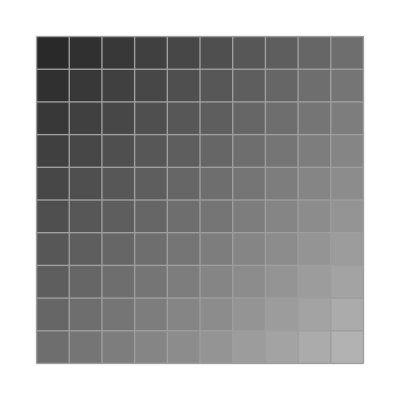

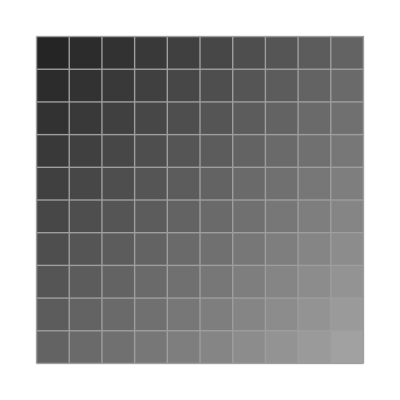

```mathematica
test1=Table[0.1+0.03*i+0.03*j,{i,1,10},{j,1,10}];
test2=test1*0.9;
ArrayPlot[test1,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,1},Mesh->True]
ArrayPlot[test2,ColorFunction->(Blend[{Black,White},#]&),PlotRange->{0,1},Mesh->True]
```

```mathematica
ArrayPlot[bgrid[[-1]]]
```

(0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851
0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851 | 0.0262851)